3727.43

3727.38

3727.43

Total Width q2=214348.

Total Width q =214348.

Phace Space q2 =1.16618×10^-6

dgdq2[mx2] = 0.000419267

me2[mx2] = 4.58006×10^13

phs[mx2]  = 0.0000283679

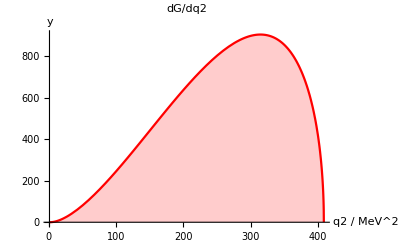

NormONE=0.0000569515

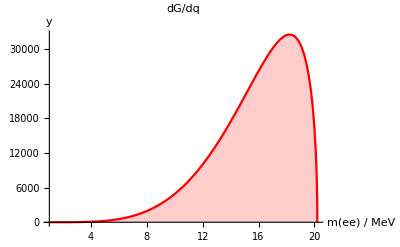

NormME2=16 π^2

-Graphics-

NormPHSP=3.58811×10^-11

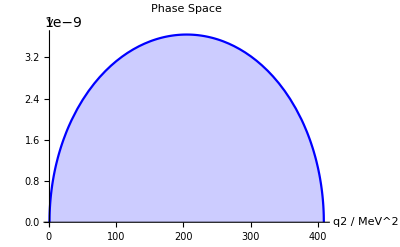

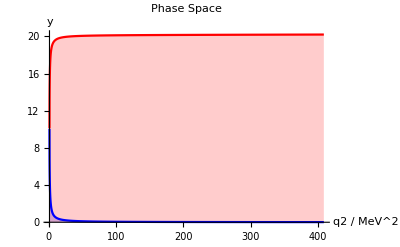

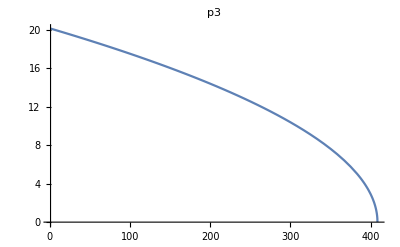

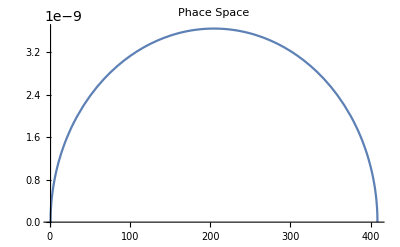

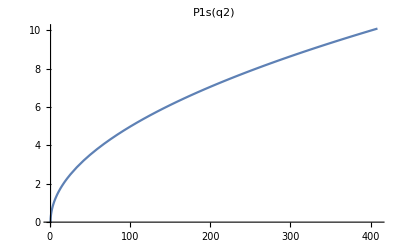

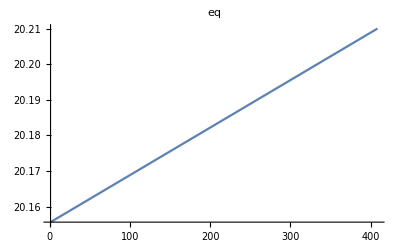

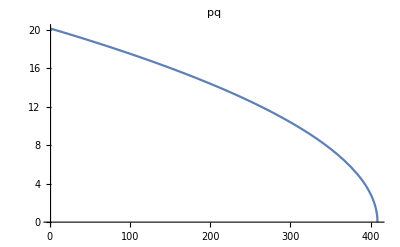

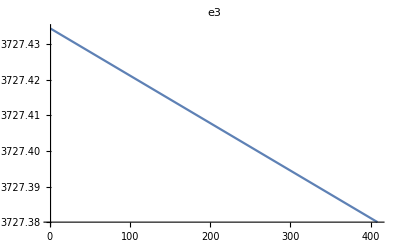

```mathematica
mbe8=8.005305*931.5;
mbe8s=mbe8+18.15;
mhe4=3727.38;
mhe4s=mhe4+20.21;
me= 0.00051099907*1000;
m=mhe4s;
m3=mhe4;
me=0.51099907;
m1=me;
q2min=(2me)^2;
q2max=(m-m3)^2;
qmin=2 me;
qmax=m-m3;

eq[q2_]:=(m^2-m3^2+q2)/(2m);
pq[q2_]:=Sqrt[eq[q2]^2-q2];
p3[q2_]:=pq[q2];
p31[q2_]:=Sqrt[(m^2-(Sqrt[q2]+m3)^2)*(m^2-(Sqrt[q2]-m3)^2)]/(2*m);

e3[q2_]:=Sqrt[p3[q2]^2+m3^2];
p1s[q2_]:=Sqrt[q2/4-me^2];
e1s[q2_]:=Sqrt[q2]/2;
gamma[q2_]:=eq[q2]/Sqrt[q2];
vel[q2_]:=Sqrt[eq[q2]^2-q2]/eq[q2];
e1min[q2_]:=gamma[q2]*(e1s[q2]-p1s[q2]);
e1max[q2_]:=gamma[q2]*(e1s[q2]+p1s[q2]);
e3min=e3[q2max];
e3max=e3[q2min];
p3q[q2_]:=(m^2-m3^2-q2)/2.;
p1q[q2_]:=q2/2.;
p1p2[q2_]:=(q2-2me^2)/2.;
p3p1[q2_]:=m*gamma[q2]*Sqrt[q2]/2;
me2[q2_]:=(4 Pi)^2*(2*( (m*gamma[q2])^2 *(e1s[q2]^2-(vel[q2]*p1s[q2]*2/3))^2)-m3^2*(q2-2me^2)/2-me^2*m3^2);
phs[q2_]:= p3[q2]*p1s[q2];




normphsp=1./(2*Pi)^5/(16*m^2)*4*Pi*2*Pi;
normme2=(4*Pi)^2;
normone=8*Pi/(m^5*5.97*10^(-13));
norm=normphsp*normme2*normone;
dgdq2[q2_]:=me2[q2]*phs[q2]*norm;
dgdq[q_]    :=me2[q^2]*phs[q^2]*2*q*norm;



Print["Total Width q2=",NIntegrate[dgdq2[q2],{q2,q2min,q2max}]]
Print["Total Width q =",NIntegrate[dgdq[q],{q,qmin,qmax}]]
Print["Phace Space q2 =",NIntegrate[phs[q2]*normphsp,{q2,q2min,q2max}]]

mx2=q2max;
Print["dgdq2[mx2] = ",dgdq2[mx2]]
Print["me2[mx2] = ",  me2[mx2]]
Print["phs[mx2]  = ",phs[mx2]]

Plot[dgdq2[q2],                     {q2,q2min,q2max},
PlotLabel->"dG/dq2",
FrameLabel->{"q2/MeV^2","dG/dq2"},
PlotRange->{{q2min,q2max},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"q2 / MeV^2",y},
PlotStyle->{Blue,Red}
]
Print["NormONE=",normone]
Plot[dgdq[q],                     {q,qmin,qmax},
PlotLabel->"dG/dq",
FrameLabel->{"m(ee)/MeV","dG/dm(ee)"},
PlotRange->{{qmin,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Blue,Red}
]
Print["NormME2=",normme2]
Plot[me2[q2]*normme2,                   {q2,q2min,q2max},
PlotLabel->"|M|^2",
FrameLabel->{"q2/MeV^2","dG/dq2"},
PlotRange->{{q2min,q2max},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"q2 / MeV^2",y},
PlotStyle->{Blue}
]
Print["NormPHSP=",normphsp]
Plot[phs[q2]*normphsp,                   {q2,q2min,q2max},
PlotLabel->"Phase Space",
FrameLabel->{"q2/MeV^2","dG/dq2"},
PlotRange->{{q2min,q2max},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"q2 / MeV^2",y},
PlotStyle->{Blue}
]

Plot[{e1min[q2],e1max[q2]},                   {q2,q2min,q2max},
PlotLabel->"Phase Space",
FrameLabel->{"q2/MeV^2","dG/dq2"},
PlotRange->{{q2min,q2max},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"q2 / MeV^2",y},
PlotStyle->{Blue,Red}
]

Plot[p3[q2],                    {q2,q2min,q2max},PlotLabel->"p3"]
Plot[phs[q2]*normphsp,                 {q2,q2min,q2max},PlotLabel->"Phace Space"]
Plot[p1s[q2],                  {q2,q2min,q2max},PlotLabel->"P1s(q2)"]

Plot[eq[q2],                 {q2,q2min,q2max},PlotLabel->"eq"]
Plot[pq[q2],                  {q2,q2min,q2max},PlotLabel->"pq"]

Plot[e3[q2],                   {q2,q2min,q2max},PlotLabel->"e3"]
Plot[e1min[q2],                   {q2,q2min,q2max},PlotLabel->"e1_min"]
Plot[e1max[q2],                   {q2,q2min,q2max},PlotLabel->"e1_max"]

Plot[gamma[q2],             {q2,q2min,q2max},PlotLabel->"gamma"]
Plot[vel[q2],                  {q2,q2min,q2max},PlotLabel->"velocity"]
Plot[p3q[q2],                  {q2,q2min,q2max},PlotLabel->"p3q"]
Plot[p3p1[q2],                {q2,q2min,q2max},PlotLabel->"p3p1"]
Plot[p1q[q2],                    {q2,q2min,q2max},PlotLabel->"p1q"]
```

```mathematica
m1
```

0.510999

```mathematica
m1
```

0.510999

```mathematica
me
```

0.510999

```mathematica
dgdq[qmax]
```

3.48072×10^19

```mathematica
norm
```

441301.